```mathematica
(* Set Up Computer Options *) 
SetDirectory[NotebookDirectory[]];
CreateDirectory["results_amolf"];

(*Set Up Computer Options*)
numkernel=4;
Unprotect[$ProcessorCount];
$ProcessorCount=numkernel;
$HistoryLength=0
```

CreateDirectory::eexist: /Users/tomikbaikie/Dropbox (Cambridge University)/Physics/SimulationsLSC/Example_simulation/combined_LSC_directional/results_amolf already exists.

0

```mathematica
(* Set Up Raytracing Options *)
```

```mathematica
sides=4;
anglestart=1;
angleend=90;
numberofphotons=10000;

numberofangles=89;
totalphotonsin=numberofphotons;
cell=13;
```

```mathematica
(* Set Up Simulation Options *)
```

```mathematica
(* ----- Notebook Running Running ----- *) 

(*dayinyear=ToExpression[70];
startwavelength=ToExpression[320];
endwavelength=ToExpression[550];
timestepsize=60;
days=100;*)

(*LSC orientation; vector defining its surface normal in degrees*)
lscAltitude=0 ;(*0 is horizontal, 90 is vertical up*)
lscAzimuth = 180;(*0 is facing North, 180 is facing South*)
ClearSystemCache[]; 


(* ----- Command Line Running ----- *) 
days = 180;
```

```mathematica
(* Import or Create Raytracing Results *)
```

```mathematica
(* Raytracing Data *)
```

```mathematica
(* import datastore *) 

Import["./raytracing.mx"]
(*minimumwavelength*)
emissionmax=N[1200];
emissionmin=N[311];
wavelengthtable=Table[{N[x],0},{x,emissionmin,emissionmax,1}];
```

```mathematica
Dimensions[raytracingdata]
```

{4,90,890}

```mathematica
daysinmonth ={31,28,31,16,31,30,31,31,21,31,30,31};

Which[1<=days<=Total[daysinmonth[[1]]],Print["jan"];monthvalue=1;,
Total[daysinmonth[[1]]]<days<=Total[daysinmonth[[1;;2]]],Print["feb"];monthvalue=2;,
Total[daysinmonth[[1;;2]]]<days<=Total[daysinmonth[[1;;3]]],Print["march"];monthvalue=3;,
Total[daysinmonth[[1;;3]]]<days<=Total[daysinmonth[[1;;4]]],Print["apr"];monthvalue=4;,
Total[daysinmonth[[1;;4]]]<days<=Total[daysinmonth[[1;;5]]],Print["may"];monthvalue=5;,
Total[daysinmonth[[1;;5]]]<days<=Total[daysinmonth[[1;;6]]],Print["jun"];monthvalue=6;,
Total[daysinmonth[[1;;6]]]<days<=Total[daysinmonth[[1;;7]]],Print["july"];monthvalue=7;,
Total[daysinmonth[[1;;7]]]<days<=Total[daysinmonth[[1;;8]]],Print["aug"];monthvalue=8;,
Total[daysinmonth[[1;;8]]]<days<=Total[daysinmonth[[1;;9]]],Print["sept"]; monthvalue=9,
Total[daysinmonth[[1;;9]]]<days<=Total[daysinmonth[[1;;10]]],Print["oct"];monthvalue=10;,
Total[daysinmonth[[1;;10]]]<days<=Total[daysinmonth[[1;;11]]],Print["nov"];monthvalue=11;,
Total[daysinmonth[[1;;11]]]<days<=Total[daysinmonth[[1;;12]]],Print["dec"];monthvalue=12;];

daystartingpoint = days -Total[daysinmonth[[;;monthvalue-1]]];
timepoint = 1+(daystartingpoint-1)*8640;
```

july

```mathematica
(* Import Spectra Data  *)
```

```mathematica
(*Import LAD data for 2019*)
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/tomikbaikie/Dropbox (Cambridge University)/Physics/SimulationsLSC/Example_simulation/combined_LSC_directional

```mathematica
LADData=FileNames["./training_rules/LAD2019_07.mx"]; (*All LAD data for 2019. One file for each month. Date is in absolute time, the twelve following numbers are the LAD sensors. 
This data is not yet calibrated and has to be calibrated with the listCalibrate function below, since the neural network has been trained on calibrated data.*)
(*Import one LAD dataset for test purposes*)
monthdatalad =Import[LADData[[1]]];
wavelengths=Import["./machine_fluff/wavelengthsSpectrometer.mx"];(*The x-Axis for the result of the training network*)
trainedNet1=Import["./machine_fluff/bestnet.wlnet"];(*Import the best training network, trained for 400 rounds on the year 2019. 
The neural net is: Input, Linearlayer5, ConstantLayer, Linearlayer 2048, Abs, Output. Please see training notebook and powerpoint presentation for details.*)
calibrationImport=Import["./machine_fluff/calibrationTable.mx"];(*Calibration of the LAD sensor data to W/m^2. Calibrated with a solar simulator at amolf by bachelor student A.Pollastri. 
The solar simulator is set to different intensities and the 12 sensors held at different temperatures, such that *)
SensorToWm2[sensorNr_,color_,sensor1_,temp1_]:=calibrationImport[[sensorNr,color]]/.sensor->sensor1/.temp->temp1 (*The calibration function needs the sensor Nr, color (rgbIR), sensor Color, and temperature*)
listCalibrate[list_,sensor_]:=Module[{red,green,blue,IR,temp},
{red,green,blue,IR,temp}=list;

{SensorToWm2[sensor,1,red,temp],
SensorToWm2[sensor,2,green,temp],
SensorToWm2[sensor,3,blue,temp],
SensorToWm2[sensor,4,IR,temp],
temp}
];
(* see additional documentation for how anglular dependence from the LAD is determined *) 
(*Mix the 12  spectra into one:
ATTENTION: IN NORMAL ALTITUDE ANGLES*)
sphericaltoCartesian[θ_,ϕ_]=CoordinateTransform["Spherical"->"Cartesian",{1,θ,ϕ}];
mathDodetoRealDodeAssoc=Association[4->"A",2->"F",3->"B",11->"C",12->"D",5->"E",9->"L",7->"K",10->"J",1->"I",8->"H",6->"G"];
polygonPoints[polygon_]:=N[polygon[[1]]]
normalVector[list_]:=Module[{p1,p2,p3},
{p1,p2,p3}=list[[;;3]];
Cross[p2-p1,p3-p1]
];
polyhedronPolygonList=PolyhedronData["Dodecahedron","Polygons"];
normalArrow[polygon_]:=Arrow[{RegionCentroid[N@polygon],RegionCentroid[N@polygon]+normalVector[polygonPoints[polygon]]}];
degToRad[angle_] := angle π/180.
azimuthToPhi[azi_]:=azi+90.
altitudeToTheta[alt_]:=90.-alt
(* see additional documentation for how anglular dependence from the LAD is determined *) 
rotation=Composition[RotationTransform[degToRad[30],{1,0,0}],RotationTransform[degToRad[-90],{0,0,1}]];
realNormalVectors=Table[normalVector[polygonPoints[Normal[GeometricTransformation[polyhedronPolygonList[[side]],rotation]]]],{side,Range[12]}][[Keys[Sort[mathDodetoRealDodeAssoc]]]];
normDot[a_,b_]:=a.b/(Norm[a]Norm[b])
normDotSphericalOriented[number_, altitude_(**), azimuth_] := Module[{a, b},
  a = realNormalVectors[[number]];
  b = sphericaltoCartesian[degToRad[altitudeToTheta[altitude]],degToRad[azimuthToPhi[azimuth]]];
  normDot[a, b]
  ];
polyWeights[altitude_,azimuth_]:=With[
{list=Clip[normDotSphericalOriented[#,altitude,azimuth]&/@Range[12],{0,10}]},
list/Total[list]
];
angleToRad[angle_]:=angle π/180
fractionSolidAngle[x_]=Integrate[Sin[θ],{θ,0,angleToRad[x]},{ϕ,0,2π}]/(4π);
angleOpening=x/.Last@Solve[10*20==N@1/fractionSolidAngle[x],x];   //Quiet
makeSpectra[ladList_,time_,θ_,ϕ_]:={wavelengths,1/1000(*/um to /nm*) fractionSolidAngle[angleOpening]*Total[polyWeights[θ,ϕ]*Table[trainedNet1[listCalibrate[ladList[[time,2,side]],side]],{side,Range[12]}]]}ᵀ
```

```mathematica
sphericaltoCartesianLSC[θ_,ϕ_]=FromSphericalCoordinates[{1,π/180.(90.-θ),-π+2π /360.ϕ}];(*shifted to our angle definition: normal definition is theta from 0 to pi, phi from -pi to pi*)
normDot[a_,b_]:=a.b/(Norm[a]Norm[b]);(*normed dotproduct to calculate the angle between sun angle and surface normal*)
realAngleAtLSC[ altitude_, azimuth_] := (*effective angle between lsc and sun, we can do this since the lsc is symmetric in the plane*)
Module[{a, b},
a = sphericaltoCartesian[degToRad[altitudeToTheta[lscAltitude]],degToRad[azimuthToPhi[lscAzimuth]]];
b =sphericaltoCartesian[degToRad[altitudeToTheta[altitude]],degToRad[azimuthToPhi[azimuth]]];(*this is the orientation of the surface normal of the LSC*)
 ArcCos[ normDot[a, b]]180./(π)
  ];
photonsNmMConversion[data_]:={#[[1]],#[[2]]*(#[[1]] 10^(-9))/(h*c)}&/@data;
nmToeV[data_]:={fac/#[[1]],fac(*hc in units of eV x nm*)/(fac/#[[1]])^(2)(*hc/E^2*)*#[[2]](*W/m^2/nm*)}&/@data;
photonsNmMConversion[data_]:={#[[1]],#[[2]]*(#[[1]] 10^(-9))/(h*c)}&/@data;

addFourLists[{list1_,list2_,list3_,list4_}]:=If[list1[[All,1]]==list2[[All,1]]==list3[[All,1]]==list4[[All,1]],
Transpose[{list1[[All,1]],list1[[All,2]]+list2[[All,2]]+list3[[All,2]]+list4[[All,2]]}]
];
```

```mathematica
(* Constants  *)
```

```mathematica
(*Constants*)
c=299792458.;(*units:m/s*)
h=6.6260695729*10^(-34)//N; (*units:J s-Planck's Constant*)
h2=4.136*10^(-15)//N; (*units:eV s-Planck's Constant*)
q=1.60217657*10^(-19)//N; (*units:Coulombs*)
k=8.617*10^(−5)//N;(*units:eV/K*)
T=298.15//N;(*units:K*)
fac=h *c *10^(9)/q//N ;
k2=1.3807*10^(-23)//N;  (*J/K*)
ClearSystemCache[];
```

```mathematica
(* Spectra Conversion Functions   *)
```

```mathematica
(*spectra conversion functions*)
(*Function to calculate the flux of a solar spectrum*)
(*units:A/(m^2 eV)*)
makeFlux[data_]:={fac/#[[1]],(h*c)/(fac/#[[1]])^(2)*#[[1]]/(h*c)*#[[2]](*W/m^2/nm*)}&/@data;
makeFluxnm[data_]:={#[[1]],q*#[[2]]*(#[[1]] 10^(-9))/(h*c)}&/@data;
unmakeFlux[data_]:={fac/#[[1]],#[[2]]*(h*c)/(fac/#[[1]])*(fac/(fac/#[[1]]))^(2)/(h *c)}&/@data;
unmakeFluxnm[data_]:={#[[1]],#[[2]]/q*(h*c)/(#[[1]] 10^(-9))}&/@data;
```

```mathematica
(* Temperature Dependencies   *)
```

```mathematica
(*Temperature dependencies*)
(*Temperature dependent intrinsic charge carrier concentration from K.Misiakos,et al.Accurate Measurements of the Silicon Intrinsic Carrier Density from 78 to 340 K.J.Appl.Phys.1993,74,3293–3297 DOI:10.1063/1.354551*)
(*units:m^-3*)
Sini[T_Real]:=5.29*10^(19)*(T/300.)^(2.54)*Exp[-6726./T]*10^(6);

(*Temperature dependent bandgap is calculated using Varshni’s empirical equation with values from the book Physics of Semiconductor Devices Physics of Semiconductor Devices,Wiley-Interscience,1995 from Sze*)
(*units:eV*)
ClearAll[SiBandgap]
SiBandgap[Temp_Real]:=1.17-4.73*10^(-4)* Temp^(2)/(Temp+636.);

(*Temperature dependent Auger coefficient from J.Dziewior et al.Auger Coefficients for Highly Doped and Highly Excited Silicon.Appl.Phys.Lett.1977,346,11–14 DOI:10.1063/1.89694*)
(*Cn=2.8 x 10^-31 cm^6/s Cp=0.99 x 10^-31cm^6/s units:m^6/s*)
SiC[T_Real]:=(2.8 + 0.99)*10^(-43)*(T/300.)^(1./2.);
```

```mathematica
(* Current  Densities   *)
```

```mathematica
(*Current densities*)
(*Radiative recombination current density*)
JRad0Si=q*2*Pi/(c^(2)*h2^(3))*NIntegrate[En^(2)/(Exp[En/(k*T)]-1),{En,SiBandgap[T],4.4}];
JRSi[V_Real,Il_Real,Rs_Real]:=JRad0Si*(Exp[(V+Il*Rs*0.0001)/(k T)]-1);

(*Auger recombination current density*)
JRAuger[V_Real,Il_Real,Rs_Real,L_Real]:=q*L*SiC[T]*Sini[T]^3(Exp[(3 (V+Il*Rs*0.0001))/(2*k*T)]-1);

(*Non-radiative recombination current density*)
JRnon[V_Real,Il_Real,Rs_Real,INR_Real]:=INR*10^-42 Sini[T]^2(Exp[(V+Il*Rs*0.0001)/(k T)]-1);

(*Resistance*)
Resistance[V_Real,Il_Real,Rs_Real,Rsh_Real]:=(V+Il*Rs*0.0001)/(Rsh*0.0001);
```

```mathematica
(* More Constants   *)
```

```mathematica
(*Fitting values*)
(*Thickness of silicon for Auger recombination in m*)
thicknesses={(*1*)1.7*10^-4,(*2*)1.8*10^-4,(*assumption*)(*3*)1.8*10^-4,(*4*)1.9*10^-4,(*5*)1.8*10^-4,(*assumption*)(*6*)1.8*10^-4,(*assumption*)(*7*)1.9*10^-4,(*8*)1.95*10^-4,(*9*)1.5*10^-4,(*10*)2*10^-4,(*11*)1.5*10^-4,(*12*)2*10^-4,(*13*)2*10^-4};

(*Parasitic resistances in ohm cm^2*)
Rs={(*1*)1.48,(*2*)1.15,(*3*)1.35,(*4*)0.82,(*5*)1.28,(*6*)0.73,(*7*)0.59,(*8*)0.6,(*9*)0.67,(*10*)0.75,(*11*)0.47,(*12*)0.31,(*13*)0.08};
Rsh={(*1*)1800,(*2*)1300,(*3*)1800,(*4*)1800,(*5*)1200,(*6*)2000,(*7*)2000,(*8*)3000,(*9*)2000,(*10*)800,(*11*)4000,(*12*)6000,(*13*)10000};

(*Non-radiative recombination*)
INR={(*1*)58,(*2*)85.7,(*3*)56,(*4*)58,(*5*)10.5,(*6*)43,(*7*)35,(*8*)24.1,(*9*)1.5,(*10*)1.95,(*11*)1.7,(*12*)1.41,(*13*)1.88485};
```

```mathematica
(* IV Characteristics   *)
```

```mathematica
(*Import JV characteristic*)
IV13=Import["./Record_Si_cell/13_IV.csv"];
(*Import EQE*)
EQE13=Import["./Record_Si_cell/13_EQE.csv"];
intEQE13=Interpolation[EQE13,InterpolationOrder->0];
```

```mathematica
unmakeFluxnm[data_]:={#[[1]],#[[2]]/q*(h c)/(#[[1]] 10^-9)}&/@data
```

```mathematica
(* Si Effects  *)
```

```mathematica
spectraAtSolarCell[monthdata_,timestamp_,altitudePhoton_,azimuthPhoton_,rayTracingPhotons_]:=Module[{absAngle,interpolationW,interpolationPhoton,scaledCurrent,spectrum,totalspectrumW,photonsPermNm,totalPhoton,outputInterpolCurrenteV,jG,outputCurrent,outputCurrentInterpol,totalOutputCurrent,opticalEfficiency},
(* if emission max happens to be the same as one of the points in spectrum, there will be problem in interpolation, just make sure emission max is an integer *) 
spectrum=Append[makeSpectra[monthdata,timestamp,altitudePhoton,azimuthPhoton],{emissionmax,0}](*in W/m^2/nm/Xsr*);
interpolationW=Interpolation[spectrum,InterpolationOrder->0];
totalspectrumW=Integrate[interpolationW[λ],{λ,spectrum[[1,1]],spectrum[[-1,1]]}];

photonsPermNm=photonsNmMConversion[spectrum](*in photons/m^2/nm/Xsr*);
interpolationPhoton=Interpolation[photonsPermNm,InterpolationOrder->0];
totalPhoton=Integrate[interpolationPhoton[x],{x,288,emissionmax}];

absAngle =Round[90-Abs[(realAngleAtLSC[altitudePhoton,azimuthPhoton]-90)]];

(*Make output current for all four sides PER ANGLE  *)
(* this is a current flux in (*A/m^2/nm/Xsr*) *) 
scaledCurrentF[side_]:=Module[{output,result}, 
WithCleanup[
SetSystemOptions["CompileOptions"->"TableCompileLength"->Infinity],
output = Table[{wlength,q* N[interpolationPhoton[wlength]]/(N[totalphotonsin]) *Normal[raytracingdata[[side,absAngle,wlength-emissionmin+1]]]} , {wlength, emissionmin, emissionmax,1}];,
SetSystemOptions["CompileOptions"->"TableCompileLength"->250]];
(* this is just the output spectra *) 
output =output[[;;,2]];
(* result is {nm out, total} *)
result = Table[{λ,Total[output[[;;,λ-emissionmin+1]]]},{λ,wavelengthtable[[;;,1]]}];
Return[result]
];

(* add each side *) 
outputCurrent=addFourLists[{scaledCurrentF[1],scaledCurrentF[2],scaledCurrentF[3],scaledCurrentF[4]}];

(* interpolate the current, for all 4 sides, convert to W/m^2/sr*) 
outputCurrentInterpol=Interpolation[outputCurrent,InterpolationOrder->0];
totalOutputpower=NIntegrate[(N[1240/x])*outputCurrentInterpol[x],{x,outputCurrent[[1,1]],emissionmax}];

(* convert to eV -(*in A/m^2/sr*) *) 
outputInterpolCurrenteV=Interpolation[nmToeV[outputCurrent],InterpolationOrder->0];
jG=NIntegrate[intEQE13[En]*outputInterpolCurrenteV[En],{En,fac/outputCurrent[[-1,1]],fac/outputCurrent[[1,1]]},MaxRecursion->10000,WorkingPrecision->4];


{totalspectrumW,totalPhoton,totalOutputpower,jG}
]
```

```mathematica
(* old si cell if you break anything *)
```

```mathematica
sicell[areasurface_,areaside_,side_Integer,monthvalue_,pointinmonth_Integer]:=Module[{time,incidentangle,spectradirect,spectradiffuse,intspectradirect,intspectradiffuse,intfluxnmdirect,intfluxnmdiffuse,concentration,totalincidentpowerdiffuse,totalconcentratedincidentpowerdiffuse,totalincidentpowerdirect,totalconcentratedincidentpowerdirect,totalfluxdiffuse,totalfluxdirect,LSCoutputlistdirect,sidespectrafluxdirect,LSCoutputlistdiffuse,sidespectrafluxdiffuse,sidespectradirect,sidespectradiffuse,outputpowerLSCdiffuse,outputpowerLSCdirect,JG,jg,dSi,totalefficiency,outputpowerLSC,LSCefficiency,efficiency,JGdirect,LSCfluxefficiencydirect,LSCfluxefficiencydiffuse,kwhSi,kwhLSCdirect,kwhLSCdiffuse,monthdata},

(* select the data you want from the LAD *) 
monthdata =monthdatalad;
date=DateString[DateObject[monthdata[[pointinmonth,1]]]];
Print[date];
ClearSystemCache[];

(* geometric concentration *) 
concentration=N[areasurface/(4*areaside)];

(* this calculates the spectra at every angle in altitude and azimuth at up to every 10s interval throughout the year if this number of steps are changed (10 and 20) you must also change the solid angle - in the function angleopening function*) 
(* spectra at solarcell outputs {totalspectrumW,totalPhoton,totalOutputCurrent,jG} *) 
spectraAtSolarCelltemp=Flatten[Table[spectraAtSolarCell[monthdata,pointinmonth,(*angle alt*)alt,(*angle azi*)azi,totalphotonsin],{alt,1,179,180/10},{azi,1,359,360/20}],1];

(* total current density A/m^2 , from each angle *) 
jg=1 *Total[spectraAtSolarCelltemp[[All,4]]];
Print["jg:  "<>ToString[jg]];
(* total incoming power density onto the LSC *)
(* remembver, if you change the step size in alt or azi, you need to make sure that you are dealing with the solid angle incomign correctly *) 
totalIncomingPower=Total[spectraAtSolarCelltemp[[All,1]]];
Print["incoming Power:  "<>ToString[totalIncomingPower]<>"in W/m^2"];

(* calculate total power, which in W/m^2 *) 
totaloutputLSCpower=Total[spectraAtSolarCelltemp[[All,3]]];
Print["totaloutputLSCpower:  "<>ToString[totaloutputLSCpower]<>"in W/m^2"];

(*Make JV characteristic in A/m^2*)
dSi=Table[{v1,FindRoot[Il==jg-JRSi[v1,Il,Rs[[cell]]]-JRAuger[v1,Il,Rs[[cell]],thicknesses[[cell]]]-JRnon[v1,Il,Rs[[cell]],INR[[cell]]]-Resistance[v1,Il,Rs[[cell]],Rsh[[cell]]],{Il,0},PrecisionGoal->5,MaxIterations->10000][[1,2]]},{v1,0,SiBandgap[T]-0.3,.005}];
ivSi=Interpolation[dSi,InterpolationOrder->0];
(*Calculate Voc*)
vocSi=FindRoot[ivSi[v],{v,SiBandgap[T]-0.4}][[1,2]];
(*Calculate Jsc*)
jscSi=ivSi[0]/10;(*mA/cm^2*)
(*Finding the maximum power conversion efficiency of the Si cell*)
eff=NMaximize[{100*ivSi[V] *V/totalIncomingPower,0<V<SiBandgap[T]-0.3},V];
efficiency=eff[[1]];
(*efficiency of Si*)
maxvoltage=V/.eff[[2]];
maxcurrent=ivSi[maxvoltage] ;(*A/m^2*)

(* efficiency of LSC, relative to surface area *)
	(* power into the LSC vs power out of the side of LSC BEFORE impinging onto silicon cell 
	outputpower LSC is in W/(m^2) as is totalincidentpowerdirect+totalincidentpowerdiffuse*) 
	outputpowerlsc = areaside*totaloutputLSCpower;
	inputpower = (areasurface*(totalIncomingPower));
	lscPCE = outputpowerlsc/inputpower;

	(* si PCE is the PCE from the LSC output *) 
	siPCE = (maxcurrent*maxvoltage)/outputpowerlsc;


(* efficiency of LSC & Si system, relative to surface area *)
totalefficiency=(maxcurrent*maxvoltage)/(inputpower);

(* divide by 1000 for k in kwh - this much be changed if you change the step size *) 
kwh=(maxcurrent*maxvoltage)*(15/60)/1000;

Return[{month,pointinmonth,ToString[date],side,totalefficiency,lscPCE,siPCE,kwh,inputpower,outputpowerlsc,siPCE}];

];
```

```mathematica
spectrumin[monthdata_,timestamp_,altitudePhoton_,azimuthPhoton_,rayTracingPhotons_]:=Module[{absAngle,interpolationW,interpolationPhoton,scaledCurrent,spectrum,totalspectrumW,photonsPermNm,totalPhoton,outputInterpolCurrenteV,jG,outputCurrent,outputCurrentInterpol,totalOutputCurrent,opticalEfficiency},
(* if emission max happens to be the same as one of the points in spectrum, there will be problem in interpolation, just make sure emission max is an integer *) 
spectrum=Append[makeSpectra[monthdata,timestamp,altitudePhoton,azimuthPhoton],{emissionmax,0}](*in W/m^2/nm/Xsr*);
{spectrum}
]
```

```mathematica
spectrumout[monthdata_,timestamp_,altitudePhoton_,azimuthPhoton_,rayTracingPhotons_]:=Module[{absAngle,interpolationW,interpolationPhoton,scaledCurrent,spectrum,totalspectrumW,photonsPermNm,totalPhoton,outputInterpolCurrenteV,jG,outputCurrent,outputCurrentInterpol,totalOutputCurrent,opticalEfficiency,outputspectrum},
(* if emission max happens to be the same as one of the points in spectrum, there will be problem in interpolation, just make sure emission max is an integer *) 
spectrum=Append[makeSpectra[monthdata,timestamp,altitudePhoton,azimuthPhoton],{emissionmax,0}](*in W/m^2/nm/Xsr*);
interpolationW=Interpolation[spectrum,InterpolationOrder->0];
totalspectrumW=Integrate[interpolationW[λ],{λ,spectrum[[1,1]],spectrum[[-1,1]]}];

photonsPermNm=photonsNmMConversion[spectrum](*in photons/m^2/nm/Xsr*);
interpolationPhoton=Interpolation[photonsPermNm,InterpolationOrder->0];
totalPhoton=Integrate[interpolationPhoton[x],{x,288,emissionmax}];

absAngle =Round[90-Abs[(realAngleAtLSC[altitudePhoton,azimuthPhoton]-90)]];

(*Make output current for all four sides PER ANGLE  *)
(* this is a current flux in (*A/m^2/nm/Xsr*) *) 
scaledCurrentF[side_]:=Module[{output,result}, 
WithCleanup[
SetSystemOptions["CompileOptions"->"TableCompileLength"->Infinity],
output = Table[{wlength,N[interpolationPhoton[wlength]]/(N[totalphotonsin]) *Normal[raytracingdata[[side,absAngle,wlength-emissionmin+1]]]} , {wlength, emissionmin, emissionmax,1}];,
SetSystemOptions["CompileOptions"->"TableCompileLength"->250]];
(* this is just the output spectra *) 
output =output[[;;,2]];
(* result is {nm out, total} *)
result = Table[{λ,Total[output[[;;,λ-emissionmin+1]]]},{λ,wavelengthtable[[;;,1]]}];
Return[result]
];

(* add each side *) 
outputspectrum=addFourLists[{scaledCurrentF[1],scaledCurrentF[2],scaledCurrentF[3],scaledCurrentF[4]}];

{outputspectrum}
]
```

```mathematica
(* select the data you want from the LAD *) 
areasurface=(10*10^(-2))^2;
areaside=10*1/3*(10^(-2))^2;
side =1; (* not needed*)
monthvalue =7;
pointinmonth=13000; 

monthdata =monthdatalad;
date=DateString[DateObject[monthdata[[pointinmonth,1]]]];
Print[date];
ClearSystemCache[];
```

Tue 2 Jul 2019 12:06:32

```mathematica
(* geometric concentration *) 
concentration=N[areasurface/(4*areaside)];
```

```mathematica
(* this calculates the spectra at every angle in altitude and azimuth at up to every 10s interval throughout the year if this number of steps are changed (10 and 20) you must also change the solid angle - in the function angleopening function*) 
(* spectra at solarcell outputs {totalspectrumW,totalPhoton,totalOutputCurrent,jG} *) 
spectraAtSolarCelltemp=Flatten[Table[spectraAtSolarCell[monthdata,pointinmonth,(*angle alt*)alt,(*angle azi*)azi,totalphotonsin],{alt,1,179,180/10},{azi,1,359,360/20}],1];
```

```mathematica
spectraAtSolarCelltempforplot=Flatten[Table[{alt,azi,spectraAtSolarCell[monthdata,pointinmonth,(*angle alt*)alt,(*angle azi*)azi,totalphotonsin]},{alt,1,179,180/10},{azi,1,359,360/20}],1]
```

{{1,1,{0.366044,1.21905×10^18,0.219308,0.1671}},{1,19,{0.293608,9.74684×10^17,0.176141,0.1342}},{1,37,{0.201823,6.66543×10^17,0.121328,0.09242}},{1,55,{0.207435,6.90689×10^17,0.124333,0.09472}},{1,73,{0.222678,7.47226×10^17,0.133089,0.1014}},{1,91,{0.27281,9.20967×10^17,0.162717,0.124}},{1,109,{0.532623,1.79595×10^18,0.317939,0.2422}},{1,127,{0.767185,2.58586×10^18,0.458078,0.349}},{1,145,{1.01838,3.43132×10^18,0.60819,0.4633}},{1,163,{1.21831,4.10608×10^18,0.727474,0.5542}},{1,181,{1.40486,4.73894×10^18,0.8385,0.6388}},{1,199,{1.59573,5.3864×10^18,0.952098,0.7253}},{1,217,{1.67391,5.65371×10^18,0.998411,0.7606}},{1,235,{1.51118,5.10725×10^18,0.900982,0.6864}},{1,253,{1.36205,4.60646×10^18,0.811684,0.6184}},{1,271,{1.18738,4.01969×10^18,0.707121,0.5387}},{1,289,{0.980842,3.31477×10^18,0.584458,0.4453}},{1,307,{0.800053,2.69728×10^18,0.477123,0.3635}},{1,325,{0.59173,1.9854×10^18,0.353487,0.2693}},{1,343,{0.438521,1.46358×10^18,0.262498,0.2}},{19,1,{0.519862,1.74463×10^18,0.321311,0.2449}},{19,19,{0.457547,1.53478×10^18,0.282898,0.2156}},{19,37,{0.367618,1.23359×10^18,0.22731,0.1732}},{19,55,{0.291823,9.80712×10^17,0.180408,0.1375}},{19,73,{0.42168,1.41744×10^18,0.260757,0.1987}},{19,91,{0.603369,2.02879×10^18,0.373116,0.2843}},{19,109,{0.812089,2.73219×10^18,0.501997,0.3826}},{19,127,{1.02756,3.45783×10^18,0.635111,0.484}},{19,145,{1.29002,4.3412×10^18,0.797313,0.6076}},{19,163,{1.61217,5.43545×10^18,0.995475,0.7586}},{19,181,{1.80779,6.09953×10^18,1.11581,0.8503}},{19,199,{1.99474,6.73394×10^18,1.23083,0.938}},{19,217,{2.06016,6.95845×10^18,1.27079,0.9684}},{19,235,{1.88034,6.35401×10^18,1.15951,0.8836}},{19,253,{1.74777,5.90892×10^18,1.07742,0.8211}},{19,271,{1.61514,5.46372×10^18,0.995295,0.7585}},{19,289,{1.34587,4.55533×10^18,0.829017,0.6318}},{19,307,{1.05258,3.56294×10^18,0.648193,0.494}},{19,325,{0.789844,2.66373×10^18,0.487137,0.3712}},{19,343,{0.597739,2.00768×10^18,0.369286,0.2814}},{37,1,{0.798648,2.68732×10^18,0.493382,0.3762}},{37,19,{0.76488,2.57295×10^18,0.472656,0.3604}},{37,37,{0.712862,2.39704×10^18,0.440658,0.336}},{37,55,{0.724514,2.4352×10^18,0.448033,0.3416}},{37,73,{0.796871,2.67741×10^18,0.492958,0.3759}},{37,91,{0.941335,3.16192×10^18,0.582497,0.4441}},{37,109,{1.10582,3.71623×10^18,0.684076,0.5216}},{37,127,{1.30137,4.37478×10^18,0.804876,0.6137}},{37,145,{1.55218,5.2213×10^18,0.95966,0.7317}},{37,163,{1.81335,6.10969×10^18,1.12018,0.8541}},{37,181,{2.04256,6.89015×10^18,1.26097,0.9615}},{37,199,{2.26812,7.65759×10^18,1.39957,1.067}},{37,217,{2.40241,8.11453×10^18,1.48205,1.13}},{37,235,{2.26882,7.66602×10^18,1.39932,1.067}},{37,253,{2.15276,7.27647×10^18,1.32745,1.012}},{37,271,{1.99833,6.75597×10^18,1.23203,0.9394}},{37,289,{1.64313,5.55348×10^18,1.01308,0.7725}},{37,307,{1.35329,4.5708×10^18,0.834575,0.6364}},{37,325,{1.10617,3.73135×10^18,0.682548,0.5204}},{37,343,{0.890834,2.99791×10^18,0.550265,0.4196}},{55,1,{1.24214,4.17728×10^18,0.0798523,0.06071}},{55,19,{1.15675,3.88959×10^18,0.0743684,0.05654}},{55,37,{1.10039,3.69941×10^18,0.0707497,0.05379}},{55,55,{1.10337,3.70872×10^18,0.0709452,0.05394}},{55,73,{1.16334,3.90959×10^18,0.0748032,0.05688}},{55,91,{1.28537,4.31908×10^18,0.0826504,0.06284}},{55,109,{1.40756,4.73012×10^18,0.0905014,0.06881}},{55,127,{1.55545,5.2279×10^18,0.100003,0.07604}},{55,145,{1.71014,5.75436×10^18,0.109902,0.08356}},{55,163,{1.86289,6.27499×10^18,0.119671,0.09099}},{55,181,{2.01438,6.79084×10^18,0.129364,0.09836}},{55,199,{2.16241,7.29445×10^18,0.138837,0.1056}},{55,217,{2.30447,7.77726×10^18,0.147933,0.1125}},{55,235,{2.36943,7.9989×10^18,0.152086,0.1156}},{55,253,{2.25251,7.60514×10^18,0.144577,0.1099}},{55,271,{2.08098,7.02555×10^18,0.133573,0.1016}},{55,289,{1.82682,6.16572×10^18,0.117276,0.08917}},{55,307,{1.61792,5.45765×10^18,0.103889,0.07899}},{55,325,{1.44897,4.88352×10^18,0.0930727,0.07076}},{55,343,{1.3199,4.44291×10^18,0.084822,0.06449}},{73,1,{1.61932,5.44836×10^18,0.993144,0.7566}},{73,19,{1.55054,5.2139×10^18,0.95126,0.7247}},{73,37,{1.51263,5.08484×10^18,0.928172,0.7071}},{73,55,{1.51117,5.07954×10^18,0.92734,0.7065}},{73,73,{1.54966,5.20853×10^18,0.951026,0.7245}},{73,91,{1.62822,5.47224×10^18,0.999305,0.7613}},{73,109,{1.70542,5.7338×10^18,1.0465,0.7973}},{73,127,{1.76277,5.92998×10^18,1.08137,0.8238}},{73,145,{1.83252,6.16809×10^18,1.12382,0.8562}},{73,163,{1.90911,6.42921×10^18,1.17047,0.8917}},{73,181,{1.98775,6.69703×10^18,1.2184,0.9282}},{73,199,{2.0641,6.95673×10^18,1.26495,0.9637}},{73,217,{2.13378,7.19347×10^18,1.30747,0.9961}},{73,235,{2.19206,7.39113×10^18,1.34306,1.023}},{73,253,{2.23358,7.53146×10^18,1.36846,1.043}},{73,271,{2.16402,7.2964×10^18,1.32586,1.01}},{73,289,{2.02124,6.8137×10^18,1.23848,0.9435}},{73,307,{1.90285,6.41254×10^18,1.1661,0.8884}},{73,325,{1.81241,6.10507×10^18,1.11092,0.8464}},{73,343,{1.71512,5.7742×10^18,1.05158,0.8011}},{91,1,{1.92329,6.4759×10^18,0.614445,0.468}},{91,19,{1.92734,6.48969×10^18,0.615729,0.469}},{91,37,{1.92931,6.49647×10^18,0.616352,0.4694}},{91,55,{1.92902,6.49557×10^18,0.616254,0.4694}},{91,73,{1.92649,6.48709×10^18,0.615446,0.4687}},{91,91,{1.92199,6.47188×10^18,0.614008,0.4676}},{91,109,{1.91595,6.45144×10^18,0.612083,0.4662}},{91,127,{1.90897,6.42778×10^18,0.609859,0.4645}},{91,145,{1.90172,6.40322×10^18,0.607553,0.4627}},{91,163,{1.89492,6.38013×10^18,0.605391,0.4611}},{91,181,{1.88923,6.36078×10^18,0.603582,0.4597}},{91,199,{1.8852,6.34703×10^18,0.602303,0.4587}},{91,217,{1.88322,6.34023×10^18,0.601677,0.4583}},{91,235,{1.88349,6.34106×10^18,0.601767,0.4583}},{91,253,{1.88598,6.34942×10^18,0.602565,0.4589}},{91,271,{1.89046,6.36454×10^18,0.603994,0.46}},{91,289,{1.89648,6.38493×10^18,0.605915,0.4615}},{91,307,{1.90347,6.40861×10^18,0.608142,0.4632}},{91,325,{1.91074,6.43326×10^18,0.610455,0.4649}},{91,343,{1.91757,6.45645×10^18,0.612627,0.4666}},{109,1,{1.9908,6.70779×10^18,1.23276,0.9393}},{109,19,{2.07529,6.99518×10^18,1.28481,0.979}},{109,37,{2.15284,7.25868×10^18,1.33262,1.015}},{109,55,{2.2185,7.48135×10^18,1.37313,1.046}},{109,73,{2.26637,7.6432×10^18,1.40272,1.069}},{109,91,{2.15424,7.26451×10^18,1.33333,1.016}},{109,109,{1.99781,6.73561×10^18,1.23661,0.9422}},{109,127,{1.86825,6.29657×10^18,1.15659,0.8813}},{109,145,{1.76858,5.95775×10^18,1.09515,0.8345}},{109,163,{1.69199,5.69622×10^18,1.04804,0.7986}},{109,181,{1.58464,5.33115×10^18,0.981895,0.7482}},{109,199,{1.50745,5.06802×10^18,0.934402,0.712}},{109,217,{1.46284,4.91751×10^18,0.90682,0.691}},{109,235,{1.46165,4.91308×10^18,0.906155,0.6904}},{109,253,{1.50319,5.05228×10^18,0.931982,0.7101}},{109,271,{1.588,5.33696×10^18,0.98464,0.7502}},{109,289,{1.67538,5.6317×10^18,1.03874,0.7915}},{109,307,{1.74067,5.855×10^18,1.07885,0.822}},{109,325,{1.81881,6.12175×10^18,1.1269,0.8586}},{109,343,{1.90384,6.41163×10^18,1.17922,0.8985}},{127,1,{2.01733,6.80125×10^18,0.920465,0.7011}},{127,19,{2.1734,7.33221×10^18,0.991333,0.755}},{127,37,{2.32401,7.84411×10^18,1.05976,0.8072}},{127,55,{2.37071,8.00423×10^18,1.08086,0.8232}},{127,73,{2.24821,7.59166×10^18,1.02491,0.7806}},{127,91,{2.07208,6.99651×10^18,0.944614,0.7195}},{127,109,{1.80658,6.09826×10^18,0.823658,0.6273}},{127,127,{1.58854,5.35921×10^18,0.724419,0.5517}},{127,145,{1.41117,4.75647×10^18,0.643803,0.4903}},{127,163,{1.27344,4.28643×10^18,0.581349,0.4428}},{127,181,{1.19101,4.00551×10^18,0.543968,0.4143}},{127,199,{1.11434,3.74708×10^18,0.509016,0.3877}},{127,217,{1.05759,3.55559×10^18,0.483172,0.368}},{127,235,{1.06132,3.56737×10^18,0.484962,0.3694}},{127,253,{1.12303,3.77405×10^18,0.51325,0.3909}},{127,271,{1.24845,4.1949×10^18,0.570659,0.4346}},{127,289,{1.37493,4.6204×10^18,0.628434,0.4786}},{127,307,{1.52955,5.14084×10^18,0.699038,0.5324}},{127,325,{1.69617,5.70714×10^18,0.774738,0.5901}},{127,343,{1.85773,6.25778×10^18,0.848029,0.6459}},{145,1,{2.04606,6.90248×10^18,1.26652,0.9644}},{145,19,{2.24934,7.59437×10^18,1.39174,1.06}},{145,37,{2.37167,8.01071×10^18,1.46706,1.117}},{145,55,{2.22213,7.50832×10^18,1.37423,1.046}},{145,73,{2.10413,7.11226×10^18,1.30096,0.9906}},{145,91,{1.98842,6.72366×10^18,1.22914,0.9359}},{145,109,{1.62173,5.48216×10^18,1.0025,0.7633}},{145,127,{1.32275,4.46845×10^18,0.817862,0.6227}},{145,145,{1.06628,3.59727×10^18,0.659647,0.5023}},{145,163,{0.843382,2.83852×10^18,0.522308,0.3977}},{145,181,{0.749837,2.52333×10^18,0.464431,0.3536}},{145,199,{0.718197,2.41611×10^18,0.444973,0.3388}},{145,217,{0.667846,2.24575×10^18,0.413929,0.3152}},{145,235,{0.680783,2.2882×10^18,0.422127,0.3214}},{145,253,{0.754091,2.53357×10^18,0.46777,0.3562}},{145,271,{0.900437,3.02446×10^18,0.558715,0.4254}},{145,289,{1.07054,3.59802×10^18,0.664002,0.5056}},{145,307,{1.26847,4.2646×10^18,0.786609,0.5989}},{145,325,{1.52245,5.1214×10^18,0.943816,0.7186}},{145,343,{1.80056,6.0669×10^18,1.11528,0.8492}},{163,1,{1.75937,5.93604×10^18,1.08702,0.8284}},{163,19,{1.96244,6.62479×10^18,1.21211,0.9238}},{163,37,{2.01797,6.81594×10^18,1.24599,0.9496}},{163,55,{1.83977,6.21697×10^18,1.1356,0.8655}},{163,73,{1.70541,5.7659×10^18,1.05232,0.802}},{163,91,{1.56906,5.30816×10^18,0.967807,0.7376}},{163,109,{1.2967,4.38932×10^18,0.799449,0.6093}},{163,127,{1.03221,3.49318×10^18,0.636324,0.485}},{163,145,{0.767968,2.58883×10^18,0.4742,0.3614}},{163,163,{0.579273,1.94457×10^18,0.358322,0.2731}},{163,181,{0.502008,1.68362×10^18,0.310674,0.2368}},{163,199,{0.438536,1.46983×10^18,0.271509,0.2069}},{163,217,{0.34931,1.17097×10^18,0.216299,0.1648}},{163,235,{0.259811,8.72369×10^17,0.160834,0.1226}},{163,253,{0.383859,1.29065×10^18,0.237572,0.1811}},{163,271,{0.567263,1.90777×10^18,0.351105,0.2676}},{163,289,{0.781388,2.62933×10^18,0.483464,0.3685}},{163,307,{0.998953,3.36202×10^18,0.618007,0.471}},{163,325,{1.26133,4.24516×10^18,0.780318,0.5947}},{163,343,{1.58584,5.34707×10^18,0.980155,0.747}}}

```mathematica
mwplot=Flatten[#]&/@Transpose[{spectraAtSolarCelltempforplot[[;;,{1,2}]],spectraAtSolarCelltempforplot[[;;,3,1]]}];
```

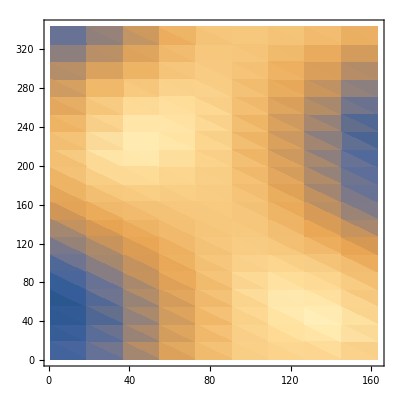

```mathematica
ListDensityPlot[mwplot]
```

```mathematica
Dimensions[map]
```

{10,20,3}

```mathematica
mwplotint=Interpolation[mwplot];
map = Table[{alt,azi,mwplotint[alt,azi]},{alt,1,179,180/10},{azi,1,359,360/20}];
Export["./plots_for_sanity/angle_imposed_map.csv",Join[{{"X","Y","Z"}},Flatten[map,1]]];
```

```mathematica
ClearAll[MPLColorMap]
<<"http://pastebin.com/raw/pFsb4ZBS";
```

Function[x,Blend[{RGBColor[{0.26700401, 0.00487433, 0.32941519}],RGBColor[{0.26851048, 0.00960483, 0.33542652}],RGBColor[{0.26994384, 0.01462494, 0.34137895}],RGBColor[{0.27130489, 0.01994186, 0.34726862}],RGBColor[{0.27259384, 0.02556309, 0.35309303}],RGBColor[{0.27380934, 0.03149748, 0.35885256}],RGBColor[{0.27495242, 0.03775181, 0.36454323}],RGBColor[{0.27602238, 0.04416723, 0.37016418}],RGBColor[{0.2770184, 0.05034437, 0.37571452}],RGBColor[{0.27794143, 0.05632444, 0.38119074}],RGBColor[{0.27879067, 0.06214536, 0.38659204}],RGBColor[{0.2795655, 0.06783587, 0.39191723}],RGBColor[{0.28026658, 0.07341724, 0.39716349}],RGBColor[{0.28089358, 0.07890703, 0.40232944}],RGBColor[{0.28144581, 0.0843197, 0.40741404}],RGBColor[{0.28192358, 0.08966622, 0.41241521}],RGBColor[{0.28232739, 0.09495545, 0.41733086}],RGBColor[{0.28265633, 0.10019576, 0.42216032}],RGBColor[{0.28291049, 0.10539345, 0.42690202}],RGBColor[{0.28309095, 0.11055307, 0.43155375}],RGBColor[{0.28319704, 0.11567966, 0.43611482}],RGBColor[{0.28322882, 0.12077701, 0.44058404}],RGBColor[{0.28318684, 0.12584799, 0.44496}],RGBColor[{0.283072, 0.13089477, 0.44924127}],RGBColor[{0.28288389, 0.13592005, 0.45342734}],RGBColor[{0.28262297, 0.14092556, 0.45751726}],RGBColor[{0.28229037, 0.14591233, 0.46150995}],RGBColor[{0.28188676, 0.15088147, 0.46540474}],RGBColor[{0.28141228, 0.15583425, 0.46920128}],RGBColor[{0.28086773, 0.16077132, 0.47289909}],RGBColor[{0.28025468, 0.16569272, 0.47649762}],RGBColor[{0.27957399, 0.17059884, 0.47999675}],RGBColor[{0.27882618, 0.1754902, 0.48339654}],RGBColor[{0.27801236, 0.18036684, 0.48669702}],RGBColor[{0.27713437, 0.18522836, 0.48989831}],RGBColor[{0.27619376, 0.19007447, 0.49300074}],RGBColor[{0.27519116, 0.1949054, 0.49600488}],RGBColor[{0.27412802, 0.19972086, 0.49891131}],RGBColor[{0.27300596, 0.20452049, 0.50172076}],RGBColor[{0.27182812, 0.20930306, 0.50443413}],RGBColor[{0.27059473, 0.21406899, 0.50705243}],RGBColor[{0.26930756, 0.21881782, 0.50957678}],RGBColor[{0.26796846, 0.22354911, 0.5120084}],RGBColor[{0.26657984, 0.2282621, 0.5143487}],RGBColor[{0.2651445, 0.23295593, 0.5165993}],RGBColor[{0.2636632, 0.23763078, 0.51876163}],RGBColor[{0.26213801, 0.24228619, 0.52083736}],RGBColor[{0.26057103, 0.2469217, 0.52282822}],RGBColor[{0.25896451, 0.25153685, 0.52473609}],RGBColor[{0.25732244, 0.2561304, 0.52656332}],RGBColor[{0.25564519, 0.26070284, 0.52831152}],RGBColor[{0.25393498, 0.26525384, 0.52998273}],RGBColor[{0.25219404, 0.26978306, 0.53157905}],RGBColor[{0.25042462, 0.27429024, 0.53310261}],RGBColor[{0.24862899, 0.27877509, 0.53455561}],RGBColor[{0.2468114, 0.28323662, 0.53594093}],RGBColor[{0.24497208, 0.28767547, 0.53726018}],RGBColor[{0.24311324, 0.29209154, 0.53851561}],RGBColor[{0.24123708, 0.29648471, 0.53970946}],RGBColor[{0.23934575, 0.30085494, 0.54084398}],RGBColor[{0.23744138, 0.30520222, 0.5419214}],RGBColor[{0.23552606, 0.30952657, 0.54294396}],RGBColor[{0.23360277, 0.31382773, 0.54391424}],RGBColor[{0.2316735, 0.3181058, 0.54483444}],RGBColor[{0.22973926, 0.32236127, 0.54570633}],RGBColor[{0.22780192, 0.32659432, 0.546532}],RGBColor[{0.2258633, 0.33080515, 0.54731353}],RGBColor[{0.22392515, 0.334994, 0.54805291}],RGBColor[{0.22198915, 0.33916114, 0.54875211}],RGBColor[{0.22005691, 0.34330688, 0.54941304}],RGBColor[{0.21812995, 0.34743154, 0.55003755}],RGBColor[{0.21620971, 0.35153548, 0.55062743}],RGBColor[{0.21429757, 0.35561907, 0.5511844}],RGBColor[{0.21239477, 0.35968273, 0.55171011}],RGBColor[{0.2105031, 0.36372671, 0.55220646}],RGBColor[{0.20862342, 0.36775151, 0.55267486}],RGBColor[{0.20675628, 0.37175775, 0.55311653}],RGBColor[{0.20490257, 0.37574589, 0.55353282}],RGBColor[{0.20306309, 0.37971644, 0.55392505}],RGBColor[{0.20123854, 0.38366989, 0.55429441}],RGBColor[{0.1994295, 0.38760678, 0.55464205}],RGBColor[{0.1976365, 0.39152762, 0.55496905}],RGBColor[{0.19585993, 0.39543297, 0.55527637}],RGBColor[{0.19410009, 0.39932336, 0.55556494}],RGBColor[{0.19235719, 0.40319934, 0.55583559}],RGBColor[{0.19063135, 0.40706148, 0.55608907}],RGBColor[{0.18892259, 0.41091033, 0.55632606}],RGBColor[{0.18723083, 0.41474645, 0.55654717}],RGBColor[{0.18555593, 0.4185704, 0.55675292}],RGBColor[{0.18389763, 0.42238275, 0.55694377}],RGBColor[{0.18225561, 0.42618405, 0.5571201}],RGBColor[{0.18062949, 0.42997486, 0.55728221}],RGBColor[{0.17901879, 0.43375572, 0.55743035}],RGBColor[{0.17742298, 0.4375272, 0.55756466}],RGBColor[{0.17584148, 0.44128981, 0.55768526}],RGBColor[{0.17427363, 0.4450441, 0.55779216}],RGBColor[{0.17271876, 0.4487906, 0.55788532}],RGBColor[{0.17117615, 0.4525298, 0.55796464}],RGBColor[{0.16964573, 0.45626209, 0.55803034}],RGBColor[{0.16812641, 0.45998802, 0.55808199}],RGBColor[{0.1666171, 0.46370813, 0.55811913}],RGBColor[{0.16511703, 0.4674229, 0.55814141}],RGBColor[{0.16362543, 0.47113278, 0.55814842}],RGBColor[{0.16214155, 0.47483821, 0.55813967}],RGBColor[{0.16066467, 0.47853961, 0.55811466}],RGBColor[{0.15919413, 0.4822374, 0.5580728}],RGBColor[{0.15772933, 0.48593197, 0.55801347}],RGBColor[{0.15626973, 0.4896237, 0.557936}],RGBColor[{0.15481488, 0.49331293, 0.55783967}],RGBColor[{0.15336445, 0.49700003, 0.55772371}],RGBColor[{0.1519182, 0.50068529, 0.55758733}],RGBColor[{0.15047605, 0.50436904, 0.55742968}],RGBColor[{0.14903918, 0.50805136, 0.5572505}],RGBColor[{0.14760731, 0.51173263, 0.55704861}],RGBColor[{0.14618026, 0.51541316, 0.55682271}],RGBColor[{0.14475863, 0.51909319, 0.55657181}],RGBColor[{0.14334327, 0.52277292, 0.55629491}],RGBColor[{0.14193527, 0.52645254, 0.55599097}],RGBColor[{0.14053599, 0.53013219, 0.55565893}],RGBColor[{0.13914708, 0.53381201, 0.55529773}],RGBColor[{0.13777048, 0.53749213, 0.55490625}],RGBColor[{0.1364085, 0.54117264, 0.55448339}],RGBColor[{0.13506561, 0.54485335, 0.55402906}],RGBColor[{0.13374299, 0.54853458, 0.55354108}],RGBColor[{0.13244401, 0.55221637, 0.55301828}],RGBColor[{0.13117249, 0.55589872, 0.55245948}],RGBColor[{0.1299327, 0.55958162, 0.55186354}],RGBColor[{0.12872938, 0.56326503, 0.55122927}],RGBColor[{0.12756771, 0.56694891, 0.55055551}],RGBColor[{0.12645338, 0.57063316, 0.5498411}],RGBColor[{0.12539383, 0.57431754, 0.54908564}],RGBColor[{0.12439474, 0.57800205, 0.5482874}],RGBColor[{0.12346281, 0.58168661, 0.54744498}],RGBColor[{0.12260562, 0.58537105, 0.54655722}],RGBColor[{0.12183122, 0.58905521, 0.54562298}],RGBColor[{0.12114807, 0.59273889, 0.54464114}],RGBColor[{0.12056501, 0.59642187, 0.54361058}],RGBColor[{0.12009154, 0.60010387, 0.54253043}],RGBColor[{0.11973756, 0.60378459, 0.54139999}],RGBColor[{0.11951163, 0.60746388, 0.54021751}],RGBColor[{0.11942341, 0.61114146, 0.53898192}],RGBColor[{0.11948255, 0.61481702, 0.53769219}],RGBColor[{0.11969858, 0.61849025, 0.53634733}],RGBColor[{0.12008079, 0.62216081, 0.53494633}],RGBColor[{0.12063824, 0.62582833, 0.53348834}],RGBColor[{0.12137972, 0.62949242, 0.53197275}],RGBColor[{0.12231244, 0.63315277, 0.53039808}],RGBColor[{0.12344358, 0.63680899, 0.52876343}],RGBColor[{0.12477953, 0.64046069, 0.52706792}],RGBColor[{0.12632581, 0.64410744, 0.52531069}],RGBColor[{0.12808703, 0.64774881, 0.52349092}],RGBColor[{0.13006688, 0.65138436, 0.52160791}],RGBColor[{0.13226797, 0.65501363, 0.51966086}],RGBColor[{0.13469183, 0.65863619, 0.5176488}],RGBColor[{0.13733921, 0.66225157, 0.51557101}],RGBColor[{0.14020991, 0.66585927, 0.5134268}],RGBColor[{0.14330291, 0.66945881, 0.51121549}],RGBColor[{0.1466164, 0.67304968, 0.50893644}],RGBColor[{0.15014782, 0.67663139, 0.5065889}],RGBColor[{0.15389405, 0.68020343, 0.50417217}],RGBColor[{0.15785146, 0.68376525, 0.50168574}],RGBColor[{0.16201598, 0.68731632, 0.49912906}],RGBColor[{0.1663832, 0.69085611, 0.49650163}],RGBColor[{0.1709484, 0.69438405, 0.49380294}],RGBColor[{0.17570671, 0.6978996, 0.49103252}],RGBColor[{0.18065314, 0.70140222, 0.48818938}],RGBColor[{0.18578266, 0.70489133, 0.48527326}],RGBColor[{0.19109018, 0.70836635, 0.48228395}],RGBColor[{0.19657063, 0.71182668, 0.47922108}],RGBColor[{0.20221902, 0.71527175, 0.47608431}],RGBColor[{0.20803045, 0.71870095, 0.4728733}],RGBColor[{0.21400015, 0.72211371, 0.46958774}],RGBColor[{0.22012381, 0.72550945, 0.46622638}],RGBColor[{0.2263969, 0.72888753, 0.46278934}],RGBColor[{0.23281498, 0.73224735, 0.45927675}],RGBColor[{0.2393739, 0.73558828, 0.45568838}],RGBColor[{0.24606968, 0.73890972, 0.45202405}],RGBColor[{0.25289851, 0.74221104, 0.44828355}],RGBColor[{0.25985676, 0.74549162, 0.44446673}],RGBColor[{0.26694127, 0.74875084, 0.44057284}],RGBColor[{0.27414922, 0.75198807, 0.4366009}],RGBColor[{0.28147681, 0.75520266, 0.43255207}],RGBColor[{0.28892102, 0.75839399, 0.42842626}],RGBColor[{0.29647899, 0.76156142, 0.42422341}],RGBColor[{0.30414796, 0.76470433, 0.41994346}],RGBColor[{0.31192534, 0.76782207, 0.41558638}],RGBColor[{0.3198086, 0.77091403, 0.41115215}],RGBColor[{0.3277958, 0.77397953, 0.40664011}],RGBColor[{0.33588539, 0.7770179, 0.40204917}],RGBColor[{0.34407411, 0.78002855, 0.39738103}],RGBColor[{0.35235985, 0.78301086, 0.39263579}],RGBColor[{0.36074053, 0.78596419, 0.38781353}],RGBColor[{0.3692142, 0.78888793, 0.38291438}],RGBColor[{0.37777892, 0.79178146, 0.3779385}],RGBColor[{0.38643282, 0.79464415, 0.37288606}],RGBColor[{0.39517408, 0.79747541, 0.36775726}],RGBColor[{0.40400101, 0.80027461, 0.36255223}],RGBColor[{0.4129135, 0.80304099, 0.35726893}],RGBColor[{0.42190813, 0.80577412, 0.35191009}],RGBColor[{0.43098317, 0.80847343, 0.34647607}],RGBColor[{0.44013691, 0.81113836, 0.3409673}],RGBColor[{0.44936763, 0.81376835, 0.33538426}],RGBColor[{0.45867362, 0.81636288, 0.32972749}],RGBColor[{0.46805314, 0.81892143, 0.32399761}],RGBColor[{0.47750446, 0.82144351, 0.31819529}],RGBColor[{0.4870258, 0.82392862, 0.31232133}],RGBColor[{0.49661536, 0.82637633, 0.30637661}],RGBColor[{0.5062713, 0.82878621, 0.30036211}],RGBColor[{0.51599182, 0.83115784, 0.29427888}],RGBColor[{0.52577622, 0.83349064, 0.2881265}],RGBColor[{0.5356211, 0.83578452, 0.28190832}],RGBColor[{0.5455244, 0.83803918, 0.27562602}],RGBColor[{0.55548397, 0.84025437, 0.26928147}],RGBColor[{0.5654976, 0.8424299, 0.26287683}],RGBColor[{0.57556297, 0.84456561, 0.25641457}],RGBColor[{0.58567772, 0.84666139, 0.24989748}],RGBColor[{0.59583934, 0.84871722, 0.24332878}],RGBColor[{0.60604528, 0.8507331, 0.23671214}],RGBColor[{0.61629283, 0.85270912, 0.23005179}],RGBColor[{0.62657923, 0.85464543, 0.22335258}],RGBColor[{0.63690157, 0.85654226, 0.21662012}],RGBColor[{0.64725685, 0.85839991, 0.20986086}],RGBColor[{0.65764197, 0.86021878, 0.20308229}],RGBColor[{0.66805369, 0.86199932, 0.19629307}],RGBColor[{0.67848868, 0.86374211, 0.18950326}],RGBColor[{0.68894351, 0.86544779, 0.18272455}],RGBColor[{0.69941463, 0.86711711, 0.17597055}],RGBColor[{0.70989842, 0.86875092, 0.16925712}],RGBColor[{0.72039115, 0.87035015, 0.16260273}],RGBColor[{0.73088902, 0.87191584, 0.15602894}],RGBColor[{0.74138803, 0.87344918, 0.14956101}],RGBColor[{0.75188414, 0.87495143, 0.14322828}],RGBColor[{0.76237342, 0.87642392, 0.13706449}],RGBColor[{0.77285183, 0.87786808, 0.13110864}],RGBColor[{0.78331535, 0.87928545, 0.12540538}],RGBColor[{0.79375994, 0.88067763, 0.12000532}],RGBColor[{0.80418159, 0.88204632, 0.11496505}],RGBColor[{0.81457634, 0.88339329, 0.11034678}],RGBColor[{0.82494028, 0.88472036, 0.10621724}],RGBColor[{0.83526959, 0.88602943, 0.1026459}],RGBColor[{0.84556056, 0.88732243, 0.09970219}],RGBColor[{0.8558096, 0.88860134, 0.09745186}],RGBColor[{0.86601325, 0.88986815, 0.09595277}],RGBColor[{0.87616824, 0.89112487, 0.09525046}],RGBColor[{0.88627146, 0.89237353, 0.09537439}],RGBColor[{0.89632002, 0.89361614, 0.09633538}],RGBColor[{0.90631121, 0.89485467, 0.09812496}],RGBColor[{0.91624212, 0.89609127, 0.1007168}],RGBColor[{0.92610579, 0.89732977, 0.10407067}],RGBColor[{0.93590444, 0.8985704, 0.10813094}],RGBColor[{0.94563626, 0.899815, 0.11283773}],RGBColor[{0.95529972, 0.90106534, 0.11812832}],RGBColor[{0.96489353, 0.90232311, 0.12394051}],RGBColor[{0.97441665, 0.90358991, 0.13021494}],RGBColor[{0.98386829, 0.90486726, 0.13689671}],RGBColor[{0.99324789, 0.90615657, 0.1439362}]},x]]

```mathematica
ColorFunction->MPLColorMap["Viridis"]
```

```mathematica
ColorData["Rainbow"]
```

ColorDataFunction[…]

```mathematica
ColorFunction->Function[{x,y,z,θ,Φ,r},ColorData["Rainbow"][mwplotint[θ*57.2958,Φ*57.2958]]]
```

ColorFunction→Function[{x,y,z,θ,Φ,r},ColorData[Rainbow][mwplotint[θ 57.2958,Φ 57.2958]]]

```mathematica
(* altitude is phi, theta, rho *) 
plot = SphericalPlot3D[1,{θ,0,π},{Φ,0,2 π},ColorFunction->Function[{x,y,z,θ,Φ,r},MPLColorMap["Viridis"][mwplotint[θ*57.2958,Φ*57.2958]]],PlotPoints->150,ImageSize->Large,ViewPoint -> {-2.1909975179196213, -2.3748534192073247, -1.0047890891870432}, ViewVertical -> {-0.2515365405352275, -0.21044903240021598, -0.9446907290417232}]
Export["./plots_for_sanity/sphereplot.png",plot]
```

InterpolatingFunction::dmval: Input value {0.,0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.384536,0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.769071,0.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics3D-

./plots_for_sanity/sphereplot.png

```mathematica
spectrumindata=Flatten[Table[spectrumin[monthdata,pointinmonth,(*angle alt*)alt,(*angle azi*)azi,totalphotonsin],{alt,1,179,180/10},{azi,1,359,360/20}],1];
```

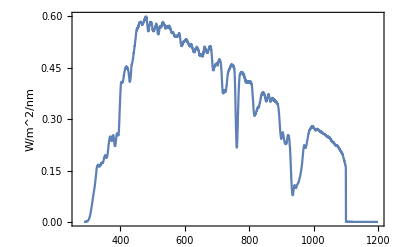

./plots_for_sanity/inputspectrum.csv

```mathematica
wavelengths1= spectrumindata[[1,1,;;,1]];
ListPlot[Transpose[{wavelengths1,Total[spectrumindata[[;;,1,;;,2]]]}],Frame->True,FrameLabel->{{"W/m^2/nm"," "},{" ","Input Spectrum"}},Joined->True]
intinputspectrum =Interpolation[Transpose[{wavelengths1,Total[spectrumindata[[;;,1,;;,2]]]}]];

Export["./plots_for_sanity/inputspectrum.csv",Transpose[{wavelengths1,Total[spectrumindata[[;;,1,;;,2]]]}]]
```

```mathematica
spectrumoutdata=Flatten[Table[spectrumout[monthdata,pointinmonth,(*angle alt*)alt,(*angle azi*)azi,totalphotonsin],{alt,1,179,180/10},{azi,1,359,360/20}],1];
```

```mathematica
wavelengths2 = spectrumoutdata[[1,1,;;,1]];
plots=Transpose[{wavelengths2,Total[spectrumoutdata[[;;,1,;;,2]]]}];
ListPlot[plots,PlotRange->All]
outputint =Interpolation[Transpose[{wavelengths2,Total[spectrumoutdata[[;;,1,;;,2]]]}]];
Export["./plots_for_sanity/photonfluxoutput.csv",Transpose[{wavelengths2,Total[spectrumoutdata[[;;,1,;;,2]]]}]]
```

-Graphics-

./plots_for_sanity/photonfluxoutput.csv

```mathematica
Plot[intinputspectrum[x]*(x*10^-9)/(h*c),{x,330,1100}]
Plot[outputint[x],{x,330,1100}]
```

-Graphics-

-Graphics-

```mathematica
(* check photon flux - per UNIT area *) 
NIntegrate[intinputspectrum[x]*(x*10^-9)/(h*c),{x,400,900}]
NIntegrate[outputint[x],{x,800,1100}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {849.211}. NIntegrate obtained 7.39277×10^20 and 3.2757×10^16 for the integral and error estimates.

7.39277×10^20

7.37321×10^20

```mathematica
NIntegrate[(10*10*10^(-2)*10^(-2))intinputspectrum[x]*(x*10^-9)/(h*c),{x,400,900}]
NIntegrate[(10*0.3*10^(-2)*10^(-2))outputint[x],{x,800,1100}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {849.211}. NIntegrate obtained 7.39277×10^18 and 3.2757×10^14 for the integral and error estimates.

7.39277×10^18

2.71003×10^17

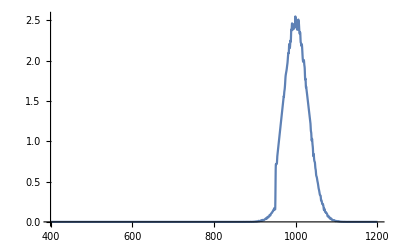

./plots_for_sanity/outputpower.csv

```mathematica
plotsint=Interpolation[plots];
Plot[plotsint[lambda]*h*c/(lambda*10^-9),{lambda,400,1200},PlotRange->All]
outputpower=Table[{x,plotsint[x]*h*c/(x*10^-9)},{x,wavelengths2}];
Export["./plots_for_sanity/outputpower.csv",outputpower]
```

```mathematica
(* total current density A/m^2 , from each angle *) 
jg=1 *Total[spectraAtSolarCelltemp[[All,4]]];
Print["jg:  "<>ToString[jg]];
(* total incoming power density onto the LSC *)
(* remembver, if you change the step size in alt or azi, you need to make sure that you are dealing with the solid angle incomign correctly *) 
totalIncomingPower=Total[spectraAtSolarCelltemp[[All,1]]];
Print["incoming Power:  "<>ToString[totalIncomingPower]<>"in W/m^2"];

(* calculate total power, which in W/m^2 *) 
totaloutputLSCpower=Total[spectraAtSolarCelltemp[[All,3]]];
Print["totaloutputLSCpower:  "<>ToString[totaloutputLSCpower]<>"in W/m^2"];

(*Make JV characteristic in A/m^2*)
dSi=Table[{v1,FindRoot[Il==jg-JRSi[v1,Il,Rs[[cell]]]-JRAuger[v1,Il,Rs[[cell]],thicknesses[[cell]]]-JRnon[v1,Il,Rs[[cell]],INR[[cell]]]-Resistance[v1,Il,Rs[[cell]],Rsh[[cell]]],{Il,0},PrecisionGoal->5,MaxIterations->10000][[1,2]]},{v1,0,SiBandgap[T]-0.3,.005}];
ivSi=Interpolation[dSi,InterpolationOrder->1];
(*Calculate Voc*)
vocSi=FindRoot[ivSi[v],{v,SiBandgap[T]-0.4}][[1,2]];
(*Calculate Jsc*)
jscSi=ivSi[0]/10;(*mA/cm^2*)
(*Finding the maximum power conversion efficiency of the Si cell*)
eff=NMaximize[{ivSi[V] *V,0<V<SiBandgap[T]-0.3},V];
efficiency=eff[[1]];
(*efficiency of Si*)
maxvoltage=V/.eff[[2]];
maxcurrent=ivSi[maxvoltage] ;(*A/m^2*)

(* efficiency of LSC, relative to surface area *)
(* power into the LSC vs power out of the side of LSC BEFORE impinging onto silicon cell  outputpower LSC is in W/(m^2) as is totalincidentpowerdirect+totalincidentpowerdiffuse*) 
outputpowerlsc = areasurface*totaloutputLSCpower;
inputpower = areasurface*(totalIncomingPower);
lscPCE = outputpowerlsc/inputpower;

(* si PCE is the PCE from the LSC output *) 
siPCE = (maxcurrent*maxvoltage)/totaloutputLSCpower;

(* efficiency of LSC & Si system, relative to surface area *)
totalefficiency=(maxcurrent*maxvoltage)/(inputpower);

(* divide by 1000 for k in kwh - this much be changed if you change the step size *) 
kwh=(maxcurrent*maxvoltage)*(15/60)/1000;
```

jg:  136.6

incoming Power:  294.098in W/m^2

totaloutputLSCpower:  179.304in W/m^2

```mathematica
totaloutputLSCpower/totalIncomingPower
```

0.609673

```mathematica
(maxcurrent*maxvoltage)/totaloutputLSCpower
```

0.456359

```mathematica
(* THE CORRECT UNIT TO USE THE POWER IN!!!!!!!!!!! PER CM^2 NOT THE AREA OF THE CELL *) 
siPCE = (0.1*0.1)*(maxcurrent*maxvoltage)/outputpowerlsc
```

0.456359

```mathematica
totalefficiency
```

27.823

```mathematica
maxcurrent*maxvoltage/outputpowerlsc
```

1369.08

```mathematica
siPCE*(4*0.1*0.0033333)*100
```

182.542

```mathematica
maxcurrent*0.1*0.1*maxvoltage
```

0.818269

```mathematica
N[areaside]
```

0.000333333

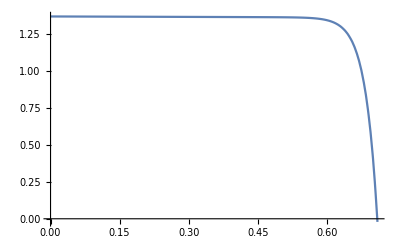

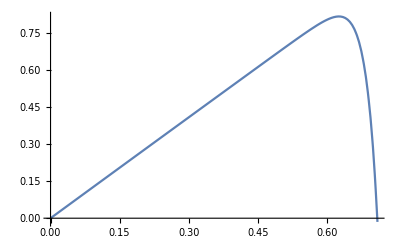

1/750

```mathematica
Plot[ivSi[x]*areasurface,{x,0,0.71},PlotRange->All]
Plot[areasurface*ivSi[x] *x,{x,0,0.71},PlotRange->All]

ivcurve=Table[{x,ivSi[x]*areasurface},{x,0,0.71,0.01}];
powercurve =Table[{x,areasurface*ivSi[x] *x},{x,0,0.71,0.01}];

Export["./plots_for_sanity/powercurve.csv",powercurve];
Export["./plots_for_sanity/ivcurve.csv",ivcurve];
```